```mathematica
(* User inputs *)
time = {0,15,40,80};
(*Probabity of AI at t[i] given no AI at t=0*)
pAI = {0,0.15, 0.5,0.67};
(* Delta final *) 
δF :=0.0001;
```

```mathematica
(* Compute transition probabilities of survival and no AI *)
pT = ConstantArray[0,Length[time]-1];
For[i=1, i<= Length[time]-1, i++, 
pT[[i]]= (1-pAI[[i+1]])/(1-pAI[[i]]);]
pT
```

{0.85,0.588235,0.66}

```mathematica
(* Suppose δ is piecewise affine*)
For[i=1, i<= Length[time]-1,i++,
	δ[i]= a[i]+b[i]*t;   δInt[i]=Integrate[δ[i], {t, time[[i]],time[[i+1]]}];
];
δ[Length[time]]= δF;
```

```mathematica
(* Boundary conditions *)
n= Length[time];
sol[n]={{a[Length[time]] ->δF,b[Length[time]] -> 0}};
For[i=1, i<= n-1, i++, sol[n-i]= NSolve[{(δ[n-i]/.t->time[[n-i+1]])== (δ[n-i+1]/.t->time[[n-i+1]]/.sol[n-i+1]), δInt[n-i]== -Log[pT[[n-i]]]},{a[n-i],b[n-i]}];
];
```

```mathematica
δ[1]
```

0.0005+t b[1]

```mathematica
sol[3]
```

{{a[3]→0.069454,b[3]→-0.000877899}}

```mathematica
(* Define δ as piecewise and plot δ *)
For[i=1, i<= Length[time],i++, δ[i]=δ[i]/.sol[i]];
δGraph = ConstantArray[t,{Length[time]-1,2 }];
For[i=1, i<=Length[time]-1,i++,δGraph[[i]][[1]] = δ[i][[1]]; δGraph[[i]][[2]]= time[[i]]<=t<=time[[i+1]]];
δPiece= Piecewise[δGraph, δ[Length[time]][[1]]];
```

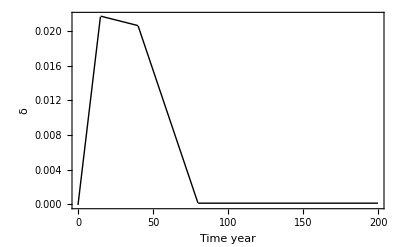

```mathematica
(* Plot δ *)
Plot[δPiece,{t,0,200}, Frame->True, FrameLabel->{Time (year), δ}, LabelStyle->{FontSize->22,FontFamily->"Times", ,Black,Bold}, PlotStyle->{Black,Thick}]
```

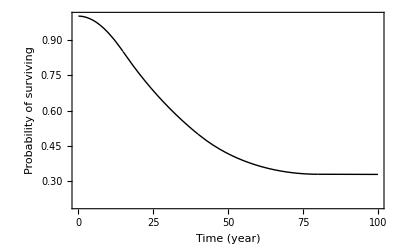

```mathematica
(* Plot probability of survival *)
δInt = Integrate[δPiece/.t->τ,{τ,0,t},Assumptions->0<=t]//FullSimplify ;
pS = Exp[-δInt];
pF = Exp[-δF*t];
Plot[pS, {t,0,100},PlotRange->{{0,100},{0.20,1}}, Frame->True, FrameLabel->{"Time (year)", "Probability of surviving"} ,LabelStyle->{FontSize->22,FontFamily->"Times", ,Black,Bold}, PlotStyle->{Black,Thick}]
```

```mathematica
(* Hamiltonian with instantaneous X-risks *)
Clear[p]
mDot = r*m - x;
pDot = -δ*p;
(*δInt = Integrate[δPiece/.t->τ,{τ,0,t},Assumptions->0<=t]//FullSimplify ;
p = Exp[-δInt]*)
H = p* x^(1-η)/(1-η)*δ+ vm*mDot+ vp*pDot
```

vm (m r-x)-p vp δ+(p x^(1-η) δ)/(1-η)

```mathematica
(* Compute optimal variables *)
xStar = SolveValues[ D[H,x] == 0, x][[1]]
vStar = DSolveValue[vm'[t]== -(D[H,m]/.vm->vm[t]), vm[t],t];
xStar = xStar/.(vm->vStar)/.C[1]-> c
```

SolveValues::ifun: Inverse functions are being used by SolveValues, so some solutions may not be found; use Reduce for complete solution information.

(vm/(p δ))^(-1/η)

((c ⅇ^(-r t))/(p δ))^(-1/η)

```mathematica
(* Compute z[n] numerically *)
$Assumptions = t∈Reals;
parameters = { r->0.05,B->100,η->2};
zI = NIntegrate[((xStar/.p->pS/.δ->δPiece)*Exp[-r*t])/.parameters/.c->1,{t,0,time[[n]]}]/.parameters
```

3.2957-0.000493572 ⅈ

```mathematica
zF =NIntegrate[(xStar*Exp[-r*t])/.p->pS/.δ->δPiece/.t->τ/.parameters/.c->1, {τ,time[[n]],Infinity}]
```

0.0310356

```mathematica
(* Compute z[t>tF] where delta is constant*)
z = B-c^(-1/η)*zI - c^(-1/η)*zF
z = z/.parameters
cTransverse = NSolveValues[z ==0, c][[1]]
```

B-(3.32674-0.000493572 ⅈ) c^(-1/η)

100-(3.32674-0.000493572 ⅈ)/(√c)

0.00110672-3.28396×10^-7 ⅈ

```mathematica
(* Compute xStar and mDot *)
xS = xStar/.(c->cTransverse)/.p->pS/.δ->δPiece ;
mD = mDot/.x->xS/.p->pS/.δ->δPiece ;
```

```mathematica
(* Solve money available *)
parameters = { r->0.03,B->100,η->2};
mStar = NDSolveValue[{m'[t]==(mD[[1]]/.m->m[t]/.parameters),m[0]==(B/.parameters)}, m[t],{t,0,200}]
```

InterpolatingFunction[…][t]

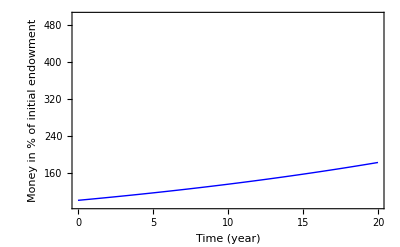

```mathematica
Plot[m[t]/.m[t]->mStar/.parameters, {t,0,20}, PlotRange->{{0,20},{90,500}}, Frame->True, FrameLabel->{"Time (year)", "Money in % of initial endowment"}, LabelStyle->{FontSize->18}, PlotStyle->{Blue,Thick}]
```

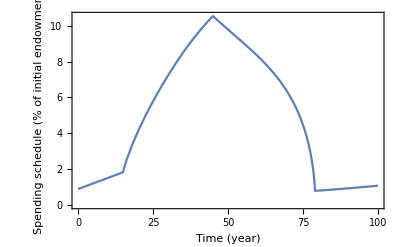

```mathematica
Plot[((xS)/. parameters), {t,0,100}, Frame->True, FrameLabel->{"Time (year)", "Spending schedule (% of initial endowment)"}]
```

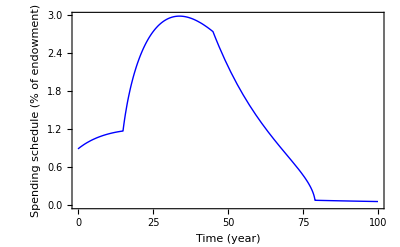

```mathematica
(* Plot spending schedule as fraction of endowment *)
Plot[((xS/m[t]*100)/.m[t]->mStar/. parameters), {t,0,100}, Frame->True, FrameLabel->{"Time (year)", "Spending schedule (% of endowment)"}, PlotStyle->{Blue,Thick}, LabelStyle->{FontSize->18}]
```

```mathematica
(* Future income: same model, new transversality condition. Write z[n], z[t>n], phi and solve conditions*)
ϕF=q*B*(δF/δInit)^γ*1/(1-Exp[-r*k]);
```

```mathematica
tF = time[[Length[time]]];
tF = IntegerPart[tF];
ϕI=Sum[q*B*((δPiece/.t->n*k)/δInit)^γ*Exp[-r*n*k], {n,0,tF}] + ϕF*(Exp[-r*tF]-1);
```

```mathematica
δInt = Integrate[δPiece/.t->τ,{τ,0,t},Assumptions->0<=t]//FullSimplify ;
pS = Exp[-δInt];
```

```mathematica
(* Define transversality condition *)
parameters =  { r->0.03,B->100,η->2,q->2,k->10, γ->0.5};
zI = NIntegrate[(Exp[-r*t/η]/(pS * δPiece)*Exp[-r*t])/.parameters,{t,0,tF}];
zF = (B - c^(-1/η)*zI + ϕI)/.parameters;
cTransverse = NSolveValues[zF==0, c][[1]]
```

52.1333

```mathematica
(* Compute xStar *)
xStarNum = xStar/.(c->cTransverse)/.p->pS/.δ->δPiece;
mDotNum = mDot/.x->xStarNum/.p->pS/.δ->δPiece;
```

```mathematica
(* Solve diff equation and plot money available *)
mStar10 = NDSolveValue[{m'[t]== (mDotNum/.m->m[t])/.parameters, m[0]==B/.parameters}, m[t],{t,0,20}];
mStar20 = NDSolveValue[{m'[t]== (mDotNum/.m->m[t])/.parameters, m[10]==((mStar10/.t->10)+ q*B)/.parameters},m[t], {t,0,20}];
```

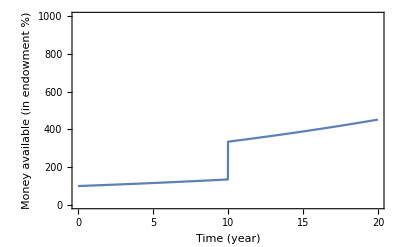

```mathematica
Plot[Piecewise[{{(mStar10/.parameters), 0<=t<10},{(mStar20/.parameters),10<=t<20}}], {t,0,20},PlotRange->{{0,20},{0,1000}},Frame->True, FrameLabel->{"Time (year)", "Money available (in endowment %)"}]
```

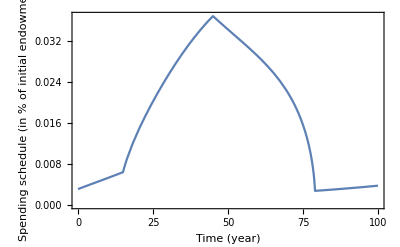

```mathematica
Plot[xStarNum/.parameters, {t,0,100}, Frame->True, FrameLabel->{"Time (year)", "Spending schedule (in % of initial endowment)"}]
```